# EIT with hyperfine states (single atom)

N.B. has not been extensively tested yet (27 Sep. 2013)

### Solve OBE for steady state

```mathematica
cst={gg->1/2,gp->2/3};
```

```mathematica
var={fsup->0.002,γp->2π 6.1,γc->2π 0.05,δc->0,hfR->2π 4,μBB->4,δp->0,Ωp->0.01,Ωc->1,δωp->0.001,δωc->0.001,f5p->0.4};
```

```mathematica
SetDirectory[NotebookDirectory[]];
obesspp=Import["obesspp.m"];
```

```mathematica
nstates=18;
ρmatrix=Table[ρ[i,j],{i,nstates},{j,nstates}];
{a, b}=CoefficientArrays[obesspp/.cst,Flatten[ρmatrix]]
```

{SparseArray[<5>, {324}],SparseArray[<1495>, {324, 324}]}

```mathematica
Export["test_b.csv", Normal[b] /.{γp->gp, γc->gc, δc->dc, μBB->muBB, δp->dp, Ωp->Wp, Ωc->Wc, δωp->dwp, δωc->dwc}]
Export["test_a.csv", Normal[a]]
```

test_b.csv

test_a.csv

#### Switch to numerics

```mathematica
AbsoluteTiming[tmp=Normal[b]/.var;]
AbsoluteTiming[solpp=LinearSolve[tmp,-a];]
```

{0.31439,Null}

{0.67417,Null}

```mathematica
cgs=Table[ClebschGordan[{2,m},{1,1},{2,m+1}],{m,-2,1}]
```

{-1/(√3),-1/(√2),-1/(√2),-1/(√3)}

```mathematica
var
```

{fsup→0.002,γp→38.3274,γc→0.314159,δc→0,hfR→8 π,μBB→4,δp→0,Ωp→0.01,Ωc→1,δωp→0.001,δωc→0.001,f5p→0.4}

{fsup→0.002,γp→38.3274,γc→0.314159,δc→0,hfR→8 π,μBB→4,δp→0,Ωp→0.01,Ωc→1,δωp→0.001,δωc→0.001,f5p→0.4}

{7.27843,Null}

{31.10499,Null}

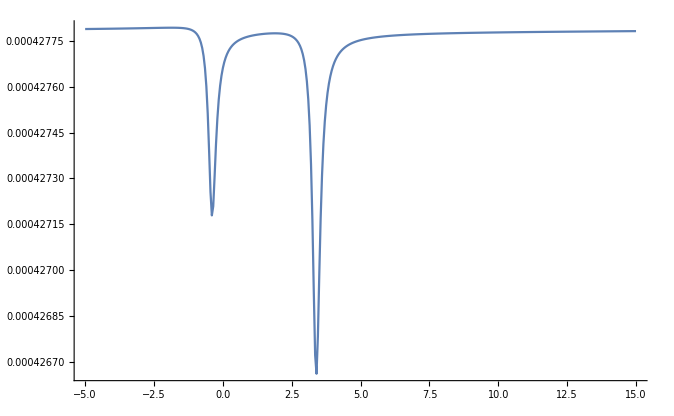

```mathematica
var
AbsoluteTiming[
cg=Table[ClebschGordan[{2,m},{1,1},{2,m+1}],{m,-2,1}];
ca2=Normal[b]/.{δc->d}/.var;
const=Normal[-a]/.var;
data=ParallelTable[{d,LinearSolve[ca2,const]},{d,-5,15,0.05}];data={#⟦1⟧,cg.Im[Table[Partition[#⟦2⟧,nstates]⟦m,m+6⟧,{m,4}]]}&/@data;]
AbsoluteTiming[
data2=ParallelTable[Solve[obesspp/.δc->d/.var/.cst],{d,-5,15,0.05}];
data2 = Flatten[1/(√3)Im[ρ[1, 7]+ρ[4, 10]] + 1/(√2)Im[ρ[2, 8] + ρ[3, 9]]/.data2];

data2 = {Table[d, {d,-5,15,0.05}], -data2}ᵀ;]
ListLinePlot[{data2}, PlotRange->All]
```

```mathematica
ρ[1, 7]/.Solve[obesspp/.δc->-5/.var/.cst]
1/(√3)(ρ[1, 7]+ρ[4, 10]) + 1/(√2)(ρ[2, 8] + ρ[3, 9])/.Solve[obesspp/.δc->-5/.var/.cst]
```

{0.0000103806-0.000149839 ⅈ}

{0.0000518936-0.000427789 ⅈ}

```mathematica
(Flatten[ρmatrix/.Solve[obesspp/.var/.cst]] - LinearSolve[ca2/.d->0, const])
LinearSolve[ca2/.d->-5, const]
```

{1.11022×10^-16+1.38791×10^-24 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.38813×10^-21-2.71051×10^-20 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.58819×10^-22+3.38813×10^-21 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,2.64698×10^-23-4.23516×10^-22 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.11022×10^-16+4.04886×10^-17 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.01644×10^-20+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.01644×10^-20+2.03288×10^-20 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.23516×10^-22+8.47033×10^-22 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.11022×10^-16+6.02969×10^-18 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.77626×10^-21-2.71051×10^-20 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,2.64698×10^-23+1.05879×10^-22 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.11022×10^-16-3.7558×10^-17 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.69407×10^-20+2.71051×10^-20 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-5.54414×10^-21 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.38813×10^-21+2.71051×10^-20 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.61744×10^-24+3.60073×10^-25 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-4.1359×10^-25-3.87741×10^-26 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.55096×10^-25-1.61559×10^-26 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+2.71051×10^-20 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-6.61744×10^-24-3.35179×10^-26 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.65436×10^-24-1.65436×10^-24 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.03398×10^-25+6.20385×10^-25 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.35525×10^-20+5.42101×10^-20 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.61744×10^-24-3.23919×10^-25 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.-5.02851×10^-26 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-3.38813×10^-21-2.71051×10^-20 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-3.30872×10^-24-7.07213×10^-25 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,5.29396×10^-23-1.69407×10^-21 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-4.1359×10^-25+6.46235×10^-26 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-9.04729×10^-26+3.27824×10^-25 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.61559×10^-26-3.47856×10^-26 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-6.77626×10^-21-2.71051×10^-20 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.65436×10^-24+1.65436×10^-24 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.65436×10^-24+5.82507×10^-25 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-2.06795×10^-25-1.19553×10^-25 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-3.97047×10^-23+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+3.23117×10^-26 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.46235×10^-27-3.44322×10^-26 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.28131×10^-26+1.09757×10^-25 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.23516×10^-22+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.03398×10^-25-4.65289×10^-25 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-2.58494×10^-25-1.32478×10^-25 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.71252×10^-25-4.96684×10^-25 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,2.64698×10^-23+2.11758×10^-22 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,7.75482×10^-26+5.31124×10^-26 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.13994×10^-26-4.10175×10^-26 ⅈ}

{0.99964+9.38947×10^-18 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.0000103806-0.000149839 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.72129×10^-7+3.47207×10^-6 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.83498×10^-8-1.18324×10^-6 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.999552+1.5872×10^-18 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.0000189948-0.0001824 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-3.21782×10^-7+4.7204×10^-6 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.24311×10^-7-1.42432×10^-6 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.999628+1.34163×10^-17 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.000025162-0.000180894 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.02791×10^-7-7.65432×10^-7 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.999863+3.75579×10^-17 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.000025421-0.000146171 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.00025+5.75344×10^-21 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.0000103806+0.000149839 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,2.25698×10^-8-7.8245×10^-26 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-5.22329×10^-10+1.02404×10^-11 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.78098×10^-10-2.03577×10^-12 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.0000189948+0.0001824 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.36493×10^-8+7.05486×10^-25 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-8.67684×10^-10+3.09854×10^-11 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,2.62319×10^-10-4.37571×10^-12 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.000025162+0.000180894 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.33715×10^-8+3.87249×10^-25 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.4112×10^-10-6.6003×10^-13 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.000025421+0.000146171 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,2.20175×10^-8+7.07562×10^-25 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.72129×10^-7-3.47207×10^-6 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-5.22329×10^-10-1.02404×10^-11 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.23135×10^-11-2.99339×10^-25 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-4.15626×10^-12-3.4063×10^-14 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-3.21782×10^-7-4.7204×10^-6 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-8.67684×10^-10-3.09854×10^-11 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,2.28399×10^-11+9.12979×10^-26 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-6.81854×10^-12-1.29351×10^-13 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.83498×10^-8+1.18324×10^-6 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.78098×10^-10+2.03577×10^-12 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-4.15626×10^-12+3.4063×10^-14 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.41463×10^-12-2.7533×10^-26 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.24311×10^-7+1.42432×10^-6 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,2.62319×10^-10+4.37571×10^-12 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-6.81854×10^-12+1.29351×10^-13 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,2.0587×10^-12+2.78999×10^-26 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.02791×10^-7+7.65432×10^-7 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.4112×10^-10+6.6003×10^-13 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,6.02652×10^-13+2.04023×10^-26 ⅈ}

### To do

choose an efficient kv-grid

identify two-photon transitions/resonances?